# Shallow-Layer Magneto-Stokes Flow (full IVP)

```mathematica
SetOptions[EvaluationNotebook[],CellProlog:>SelectionMove[NextCell[CellStyle->"Input"],All,Cell]]
```

## Deriving and nondimensionalizing the governing equations

```mathematica
Derivative/:MakeBoxes[Derivative[α__][f1_][vars__?AtomQ],TraditionalForm]:=Module[{bb,dd,sp},MakeBoxes[dd,_]^=If[Length[{α}]==1,"ⅆ","∂"];
MakeBoxes[sp,_]^=" ";
bb/:MakeBoxes[bb[x__],_]:=RowBox[Map[ToBoxes[#]&,{x}]];
TemplateBox[{ToBoxes[bb[dd^Plus[α],f1]],ToBoxes[Apply[bb,Riffle[Map[bb[dd,#]&,(Pick[{vars},#]^Pick[{α},#]&[Thread[{α}>0]])],sp]]],ToBoxes[Derivative[α][f1][vars]]},"ShortFraction",DisplayFunction:>(FractionBox[#1,#2]&),InterpretationFunction:>(#3&),Tooltip->Automatic]]
```

Define dimensional Navier Stokes

```mathematica
U={ur[t,r,θ,z],uθ[t,r,θ,z],uz[t,r,θ,z]};
gradU=Grad[U,{r,θ,z},"Cylindrical"];
strainU=gradU+gradUᵀ;
divU=Div[U,{r,θ,z},"Cylindrical"];
Id=IdentityMatrix[3];
stress=ρ0 ν strainU;
(*viscous=Div[stress,{r,θ,z},"Cylindrical"]*)
viscous=ρ0 ν Laplacian[U,{r,θ,z},"Cylindrical"];
advective=(*Div[ρ[r,θ,z]TensorProduct[U,U],{r,θ,z},"Cylindrical"]*)ρ0(D[U, t]+gradU.U);
pressure=-Grad[p[t,r,θ,z],{r,θ,z},"Cylindrical"];
gravity={0,0,-ρ0 g};
B={0,0,-b};(*let b=abs(avg(B)), and assume the field points down*)
J={ i[t]/(2π r H),0,0}+ σ Cross[U,B];
magnetism=Cross[J,B];
navierstokes=advective-pressure-viscous-gravity-magnetism;
```

Define simplifying assumptions (i.e. azimuthal symmetry of all variables)

```mathematica
assumptions={
(*Derivative[(i_/;i>0),_,_,_][___]:>(0&)(*steady*),*)
(Derivative[_,_,i_,_][___]:>(0&)/;i>0)(*axisymmetry*)
(*ur->(0&)*)
(*uz->(0&)*)
};
```

Code to convert Mathematica formatting in to human readable equations

```mathematica
cleanup={f_[t,r,θ,z]->f, 
Derivative[i_/;i>0,j_,χ_,l_][f_]->(Subscript[d, t]^i)[Derivative[0,j,χ,l][f]],
Derivative[0,j_/;j>0,χ_,l_][f_]->(Subscript[d, r]^j)[Derivative[0,0,χ,l][f]],
Derivative[0,0,χ_/;χ>0,l_][f_]->(Subscript[d, θ]^χ)[Derivative[0,0,0,l][f]],
Derivative[0,0,0,l_/;l>0][f_]->(Subscript[d, z]^l)[Derivative[0,0,0,0][f]],
ur->Subscript[u, r],
uθ->Subscript[u, θ],
uz->Subscript[u, z],
ρ0->Subscript[ρ, 0]};
```

The Dimensional Navier Stokes equations read:

```mathematica
navierstokes//.cleanup//Expand//TableForm
```

b^2 σ u_r+(ν u_r ρ_0)/r^2-(u_θ^2 ρ_0)/r+d_r[p]-(ν ρ_0 d_r[u_r])/r+u_r ρ_0 d_r[u_r]-ν ρ_0 d_r^2[u_r]+ρ_0 d_t[u_r]+u_z ρ_0 d_z[u_r]-ν ρ_0 d_z^2[u_r]+(u_θ ρ_0 d_θ[u_r])/r+(2 ν ρ_0 d_θ[u_θ])/r^2-(ν ρ_0 d_θ^2[u_r])/r^2
-(b i[t])/(2 H π r)+b^2 σ u_θ+(ν u_θ ρ_0)/r^2+(u_r u_θ ρ_0)/r-(ν ρ_0 d_r[u_θ])/r+u_r ρ_0 d_r[u_θ]-ν ρ_0 d_r^2[u_θ]+ρ_0 d_t[u_θ]+u_z ρ_0 d_z[u_θ]-ν ρ_0 d_z^2[u_θ]+d_θ[p]/r-(2 ν ρ_0 d_θ[u_r])/r^2+(u_θ ρ_0 d_θ[u_θ])/r-(ν ρ_0 d_θ^2[u_θ])/r^2
g ρ_0-(ν ρ_0 d_r[u_z])/r+u_r ρ_0 d_r[u_z]-ν ρ_0 d_r^2[u_z]+ρ_0 d_t[u_z]+d_z[p]+u_z ρ_0 d_z[u_z]-ν ρ_0 d_z^2[u_z]+(u_θ ρ_0 d_θ[u_z])/r-(ν ρ_0 d_θ^2[u_z])/r^2

### MHD-estimate scale (steady, shallow solution at surface, mid-gap)

```mathematica
shallow={
(Derivative[i_,_,_,_][___]:>(0&)/;i>0)(*steady*),
(Derivative[_,i_,_,_][___]:>(0&)/;i>0)(*shallow*),
(Derivative[_,_,i_,_][___]:>(0&)/;i>0)(*axisymmetry*),
uθ[t,r,θ,z]^(_:1) r^(_:1)->0 (*shallow*),
ur->(0&),
uz->(0&)(*no secondary flow*),
i[t]-> II (*constant current for t>0*),
σ->0(*force EM drag to vanish*)
};
```

```mathematica
shalloweqs = navierstokes//.shallow
```

{0,-(b II)/(2 H π r)-ν ρ0 uθ^(0,0,0,2)[t,r,θ,z],g ρ0+p^(0,0,0,1)[t,r,θ,z]}

```mathematica
sol = DSolve[{shalloweqs[[2]]==0,uθ[t,r,θ,0]==0,Derivative[0,0,0,1][uθ][t,r,θ,H]==0},uθ[t,r,θ,z],z];
ushallow[r_,z_] = uθ[t,r,θ,z]/.sol[[1]];
UMG = ushallow[(ri+ro)/2,H]
```

(b H II)/(2 π (ri+ro) ν ρ0)

### Nondimensionalisation

We say that every dimensional function (ur,uθ,...) of dimensional coordinates (t,r,z) is a dimensional constant (Ur,T,ro,H,...) times a non-dimensional function (uρ,uζ,...) of a non-dimensional coordinate (ρ=r/ro,...).
The notation below says what the functional relationship between dimensional and nondimensional variables is. This way, the replacement understands the chain rule.

```mathematica
nondimensionalise={
(*The dimensionless variables*)
ur->(Ur uρ[#1/T,#2/ro,#3,#4/H]&),
uθ->(Uθ uϑ[#1/T,#2/ro,#3,#4/H]&),
uz->(Uz uζ[#1/T,#2/ro,#3,#4/H]&),
p->(P ϖ[#1/T,#2/ro,#3,#4/H]&),
i->(II ι[#1/T]&),
(*The dimensionless coordinates*)
t->T τ,
r->ro ρ,
z->H ζ
};
```

Let’s separate out the dimensional equations

```mathematica
eq0=divU//.assumptions;
eq1=(navierstokes/ρ0//.assumptions)[[1]]//Simplify//Expand;
eq2=(navierstokes/ρ0//.assumptions)[[2]]//Simplify//Expand;
eq3=(navierstokes/ρ0//.assumptions)[[3]]//Simplify//Expand;
```

```mathematica
eq1
```

(ν ur[t,r,θ,z])/r^2+(b^2 σ ur[t,r,θ,z])/ρ0-uθ[t,r,θ,z]^2/r+uz[t,r,θ,z] ur^(0,0,0,1)[t,r,θ,z]-ν ur^(0,0,0,2)[t,r,θ,z]+(p^(0,1,0,0)[t,r,θ,z])/ρ0-(ν ur^(0,1,0,0)[t,r,θ,z])/r+ur[t,r,θ,z] ur^(0,1,0,0)[t,r,θ,z]-ν ur^(0,2,0,0)[t,r,θ,z]+ur^(1,0,0,0)[t,r,θ,z]

Applying the nondimensionalisation gives us:

```mathematica
ndeq0=eq0//.nondimensionalise;
ndeq1=eq1//.nondimensionalise;
ndeq2=eq2//.nondimensionalise;
ndeq3=eq3//.nondimensionalise;
```

```mathematica
ndeq1
```

-(Uθ^2 uϑ[τ,ρ,θ,ζ]^2)/(ro ρ)+(Ur ν uρ[τ,ρ,θ,ζ])/(ro^2 ρ^2)+(b^2 Ur σ uρ[τ,ρ,θ,ζ])/ρ0+(Ur Uz uζ[τ,ρ,θ,ζ] uρ^(0,0,0,1)[τ,ρ,θ,ζ])/H-(Ur ν uρ^(0,0,0,2)[τ,ρ,θ,ζ])/H^2-(Ur ν uρ^(0,1,0,0)[τ,ρ,θ,ζ])/(ro^2 ρ)+(Ur^2 uρ[τ,ρ,θ,ζ] uρ^(0,1,0,0)[τ,ρ,θ,ζ])/ro+(P ϖ^(0,1,0,0)[τ,ρ,θ,ζ])/(ro ρ0)-(Ur ν uρ^(0,2,0,0)[τ,ρ,θ,ζ])/ro^2+(Ur uρ^(1,0,0,0)[τ,ρ,θ,ζ])/T

We want to look at (and simplify) the dimensional part of each term.
We can isolate the dimensional constants by splitting up the equations and replacing all the nondimensional quantities with 1.
That’s what the conditional (/;) rules are saying below.

```mathematica
dimensionlessVars={uρ,uϑ,uζ,ϖ,ι};
dimensionlessCoords={ρ,ϑ,ζ};
reduceDimensions={f_[___]/;MemberQ[dimensionlessVars,f]->1,
Derivative[___][f_][___]/;MemberQ[dimensionlessVars,f]->1,
f_/;MemberQ[dimensionlessCoords,f]->1};
```

```mathematica
eq0dims=(List@@ndeq0)/.reduceDimensions
eq1dims=(List@@ndeq1)/.reduceDimensions
eq2dims=(List@@ndeq2)/.reduceDimensions
eq3dims=(List@@ndeq3)/.reduceDimensions
```

{Ur/ro,Uz/H,Ur/ro}

{-Uθ^2/ro,(Ur ν)/ro^2,(b^2 Ur σ)/ρ0,(Ur Uz)/H,-(Ur ν)/H^2,-(Ur ν)/ro^2,Ur^2/ro,P/(ro ρ0),-(Ur ν)/ro^2,Ur/T}

{(Uθ ν)/ro^2,(b^2 Uθ σ)/ρ0,(Ur Uθ)/ro,-(b II)/(2 H π ro ρ0),(Uz Uθ)/H,-(Uθ ν)/H^2,-(Uθ ν)/ro^2,(Ur Uθ)/ro,-(Uθ ν)/ro^2,Uθ/T}

{g,Uz^2/H,P/(H ρ0),-(Uz ν)/H^2,-(Uz ν)/ro^2,(Ur Uz)/ro,-(Uz ν)/ro^2,Uz/T}

Now that we k_now the dimensional constants in each term, we want to figure out a nice choice of scales to simplify everything.
We do this by the following replacements. Here, Re_L,γ,χ,G are dimensionless. 

If the MHD-estimate velocity scale is used, the viscosity and magnetic field are nondimensionalized as follows

```mathematica
UMG
```

(b H II)/(2 π (ri+ro) ν ρ0)

```mathematica
ReCdef = (H^2 /ν)/((ri +ro )/Uθ);
ReCFulldef = ReCdef/.{Uθ->UMG};
νscaleMHD = ν/.Solve[ReC==ReCdef ,ν][[1]];
bscaleMHD = b/.Solve[UMG==Uθ,b][[1]];
```

```mathematica
Hadef = b H √(σ/(ν ρ0));
σscale = σ/.Solve[Ha^2==Hadef^2,σ][[1]]
```

(Ha^2 ν ρ0)/(b^2 H^2)

```mathematica
Frdef =Uθ/√(g H)(*Uθ/√(g ro)*);
gscale = g/.Solve[Fr^2==Frdef^2,g][[1]];
```

```mathematica
nondimensionalisation={
T->(ri +ro )/Uθ,(*H/Ur*)
Ur->Uθ,
ν->νscaleMHD,
H->γ ro,
ri ->χ ro,
Uz->(H/ro) Uθ,
P->Uθ^2 ρ0 (*ρ0 H g*),
b->bscaleMHD,
g->gscale,
σ->σscale};
```

```mathematica
eq0dims/eq0dims[[1]]//.nondimensionalisation//Simplify
```

{1,1,1}

```mathematica
eq1dims/eq1dims[[1]]//.nondimensionalisation//Simplify
```

{1,-γ^2/(ReC+ReC χ),-Ha^2/(ReC+ReC χ),-1,1/(ReC+ReC χ),γ^2/(ReC+ReC χ),-1,-1,γ^2/(ReC+ReC χ),-1/(1+χ)}

```mathematica
eq2dims/Last[eq2dims]//.nondimensionalisation//Simplify
```

{γ^2/ReC,Ha^2/ReC,1+χ,-(1+χ)/ReC,1+χ,-1/ReC,-γ^2/ReC,1+χ,-γ^2/ReC,1}

```mathematica
eq3dims/Last[eq3dims]//.nondimensionalisation//Simplify
```

{(1+χ)/(Fr^2 γ^2),1+χ,(1+χ)/γ^2,-1/ReC,-γ^2/ReC,1+χ,-γ^2/ReC,1}

Now to print the cleaned up nondimensional equations

```mathematica
nondimcleanup={f_[τ,ρ,θ,ζ]->f,Derivative[i_/;i>0,j_,χ_,l_][f_]->(Subscript[d, t̃]^i)[Derivative[0,j,χ,l][f]],Derivative[0,j_/;j>0,χ_,l_][f_]->(Subscript[d, r̃]^j)[Derivative[0,0,χ,l][f]],Derivative[0,0,χ_/;χ>0,l_][f_]->(Subscript[d, θ]^χ)[Derivative[0,0,0,l][f]],Derivative[0,0,0,l_/;l>0][f_]->(Subscript[d, z̃]^l)[f],uρ->Subscript[ũ, r],uϑ->Subscript[ũ, θ],uζ->Subscript[ũ, z],ρ->r̃,τ->t̃,ζ->z̃,ι->ĩ,ϖ->p̃,ReC->Subscript[Re, C]};
```

```mathematica
indeq0=(ndeq0/Last[eq0dims]//Expand)//.nondimensionalisation//Simplify;
indeq0//.nondimcleanup
```

((ũ)_r)/(r̃)+d_(r̃)[(ũ)_r]+d_(z̃)[(ũ)_z]

```mathematica
indeq1=((((ReC*(ndeq1/Last[eq1dims]//Expand)//.nondimensionalisation)//Expand)//.{χ->chisub-1}//Collect[#,{ReC,chisub,γ^2}]&)//.{chisub->χ+1});

indeq1//.nondimcleanup
```

Ha^2 (ũ)_r+γ^2 (((ũ)_r)/(r̃)^2-(d_(r̃)[(ũ)_r])/(r̃)-d_(r̃)^2[(ũ)_r])+Re_C (d_(t̃)[(ũ)_r]+(1+χ) (-((ũ)_θ^2)/(r̃)+d_(r̃)[p̃]+(ũ)_r d_(r̃)[(ũ)_r]+(ũ)_z d_(z̃)[(ũ)_r]))-d_(z̃)^2[(ũ)_r]

```mathematica
indeq2=((((ReC*(ndeq2/Last[eq2dims]//Expand)//.nondimensionalisation)//Expand)//.{χ->chisub-1}//Collect[#,{ReC,chisub,γ^2}]&)//.{chisub->χ+1});
indeq2//.nondimcleanup
```

Ha^2 (ũ)_θ-((1+χ) ĩ[t̃])/(r̃)+γ^2 (((ũ)_θ)/(r̃)^2-(d_(r̃)[(ũ)_θ])/(r̃)-d_(r̃)^2[(ũ)_θ])+Re_C (d_(t̃)[(ũ)_θ]+(1+χ) (((ũ)_r (ũ)_θ)/(r̃)+(ũ)_r d_(r̃)[(ũ)_θ]+(ũ)_z d_(z̃)[(ũ)_θ]))-d_(z̃)^2[(ũ)_θ]

```mathematica
indeq3=((((ReC*(ndeq3/Last[eq3dims]//Expand)//.nondimensionalisation)//Expand)//.{χ->chisub-1}//Collect[#,{ReC,chisub,γ^2}]&)//.{chisub->χ+1});
indeq3//.nondimcleanup
```

γ^2 (-(d_(r̃)[(ũ)_z])/(r̃)-d_(r̃)^2[(ũ)_z])+Re_C (d_(t̃)[(ũ)_z]+(1+χ) ((ũ)_r d_(r̃)[(ũ)_z]+(1/Fr^2+d_(z̃)[p̃])/γ^2+(ũ)_z d_(z̃)[(ũ)_z]))-d_(z̃)^2[(ũ)_z]

Take low Ha limit:

```mathematica
fndeq0 = indeq0/.{Ha->0};
fndeq1 = indeq1/.{Ha->0};
fndeq2 = indeq2/.{Ha->0};
fndeq3 = indeq3/.{Ha->0};
pndeq0=fndeq0//.nondimcleanup;
pndeq1=fndeq1//.nondimcleanup;
pndeq2=fndeq2//.nondimcleanup;
pndeq3=fndeq3//.nondimcleanup;
```

### Printing: Stokes Operator

Dimensionless Stokes operator:

```mathematica
StokesOp[a_]:=γ^2 ρ D[1/ρ D[a,ρ],ρ]+D[a,{ζ,2}]
```

```mathematica
-fndeq1[[{1,2}]]==1/ρ StokesOp[ρ uρ[τ,ρ,θ,ζ]]//Simplify//Collect[#,γ]&
Print[HoldForm[1/ρ StokesOp[ρ uρ[τ,ρ,θ,ζ]]]//.nondimcleanup,
"         =     ",
-fndeq1[[{1,2}]]//.nondimcleanup]
```

True

StokesOp[r̃ (ũ)_r]/(r̃)         =     -γ^2 (((ũ)_r)/(r̃)^2-(d_(r̃)[(ũ)_r])/(r̃)-d_(r̃)^2[(ũ)_r])+d_(z̃)^2[(ũ)_r]

```mathematica
-fndeq2[[{2,3}]]==1/ρ StokesOp[ρ uϑ[τ,ρ,θ,ζ]]//Simplify//Collect[#,γ]&
Print[HoldForm[1/ρ StokesOp[ρ uϑ[τ,ρ,θ,ζ]]]//.nondimcleanup,
"         =     ",
-fndeq2[[{2,3}]]//.nondimcleanup]
```

True

StokesOp[r̃ (ũ)_θ]/(r̃)         =     -γ^2 (((ũ)_θ)/(r̃)^2-(d_(r̃)[(ũ)_θ])/(r̃)-d_(r̃)^2[(ũ)_θ])+d_(z̃)^2[(ũ)_θ]

```mathematica
-fndeq3[[{1,2}]]==1/ρ StokesOp[ρ uζ[τ,ρ,θ,ζ]]+(γ^2 uζ[τ,ρ,θ,ζ])/ρ^2//Simplify//Collect[#,γ]&
Print[HoldForm[1/ρ StokesOp[ρ uζ[τ,ρ,θ,ζ]]+(γ^2 uζ[τ,ρ,θ,ζ])/ρ^2]//.nondimcleanup,
"   =     ",
-fndeq3[[{1,2}]]//.nondimcleanup]
```

True

StokesOp[r̃ (ũ)_z]/(r̃)+(γ^2 (ũ)_z)/(r̃)^2   =     -γ^2 (-(d_(r̃)[(ũ)_z])/(r̃)-d_(r̃)^2[(ũ)_z])+d_(z̃)^2[(ũ)_z]

## Initial Value Problem (IVP)

```mathematica
noMeridCirc = {uρ->(0&),uζ->(0&),ι->(1&)};
magStkndeq0 = fndeq0//.noMeridCirc ;
magStkndeq1 = fndeq1//.noMeridCirc ;
magStkndeq2 = fndeq2//.noMeridCirc;
magStkndeq3 = fndeq3//.noMeridCirc ;

(*Print magneto Stokes equations:*)
Print[(0==magStkndeq0)//.nondimcleanup]
Print[(0==magStkndeq1)//.nondimcleanup]
Print[(0==magStkndeq2)//.nondimcleanup]
Print[(0==magStkndeq3)//.nondimcleanup]
```

True

0==(1+χ) Re_C (-((ũ)_θ^2)/(r̃)+d_(r̃)[p̃])

0==-(1+χ)/(r̃)+γ^2 (((ũ)_θ)/(r̃)^2-(d_(r̃)[(ũ)_θ])/(r̃)-d_(r̃)^2[(ũ)_θ])+Re_C d_(t̃)[(ũ)_θ]-d_(z̃)^2[(ũ)_θ]

0==((1+χ) Re_C (1/Fr^2+d_(z̃)[p̃]))/γ^2

```mathematica
splitcleanup={f_[τ,ρ,θ,ζ]->f,Derivative[i_/;i>0,j_,χ_,l_][f_]->(Subscript[d, t̃]^i)[Derivative[0,j,χ,l][f]],Derivative[0,j_/;j>0,χ_,l_][f_]->(Subscript[d, r̃]^j)[Derivative[0,0,χ,l][f]],Derivative[0,0,χ_/;χ>0,l_][f_]->(Subscript[d, θ]^χ)[Derivative[0,0,0,l][f]],Derivative[0,0,0,l_/;l>0][f_]->(Subscript[d, z̃]^l)[f],

f_[ρ,θ,ζ]->f,Derivative[j_/;j>0,χ_,l_][f_]->(Subscript[d, r̃]^j)[Derivative[0,χ,l][f]],Derivative[0,χ_/;χ>0,l_][f_]->(Subscript[d, θ]^χ)[Derivative[0,0,l][f]],Derivative[0,0,l_/;l>0][f_]->(Subscript[d, z̃]^l)[f],uB-> ū,uP->u',ρ->r̃,τ->t̃,ζ->z̃,ι->ĩ,ϖ->p̃,ReC->Subscript[Re, C]};
```

```mathematica
IC = uϑ[0,ρ,θ,ζ] == 0;
```

```mathematica
split = {uϑ -> (uB[#2,#3,#4]+uP[#1,#2,#3,#4]&)};
```

```mathematica
magStkUnsteady=((magStkndeq2 //.split )-(magStkndeq2 //. {uϑ -> (uB[#2,#3,#4]&)}))//FullSimplify//Apart//Collect[#,γ]&;
magStkStationary = -((magStkndeq2 //.split )-magStkUnsteady)//FullSimplify//Apart//Collect[#,γ]&;
ICUnsteadyExpr = SolveValues[(IC//.split),uP[0,ρ,θ,ζ]][[1]];

Print["Stationary:         ",(0==magStkStationary)//.splitcleanup]
Print["Time-varying:       ",(0==magStkUnsteady)//.splitcleanup]
Print["Initial condition:  ",((IC//.split//.splitcleanup)[[1]][[2]]==ICUnsteadyExpr)//.splitcleanup]
```

Stationary:         0==1/(r̃)+χ/(r̃)+γ^2 (-(ū)/(r̃)^2+(d_(r̃)[ū])/(r̃)+d_(r̃)^2[ū])+d_(z̃)^2[ū]

Time-varying:       0==γ^2 (u'/(r̃)^2-(d_(r̃)[u'])/(r̃)-d_(r̃)^2[u'])+Re_C d_(t̃)[u']-d_(z̃)^2[u']

Initial condition:  u'[0,r̃,θ,z̃]==-ū

### Stationary solution

#### Use separation of variables to obtain a modified Lommel equation

Solve  with boundary conditions

```mathematica
Stationaryndeq2func[uB_,τ_,ρ_,θ_,ζ_] = magStkStationary;
```

Assume  where the vertical eigenfunctions are chosen to satisfy the vertical boundary conditions  .

```mathematica
ansatzn[ρ_,θ_,ζ_] = un[ρ,n]*Sin[π (n-1/2)ζ];
Print[ansatzn[ρ,θ,ζ]//.nondimcleanup]
```

Sin[(-1/2+n) π z̃] un[r̃,n]

Confirm that the ansatz satisfies vertical boundary conditions:

```mathematica
0==ansatzn[ρ,θ,ζ]/.{ζ->0}//Simplify[#,Element[n,Integers]]&
0==D[ansatzn[ρ,θ,ζ],ζ]/.{ζ->1}//Simplify[#,Element[n,Integers]]&
```

True

True

Expand the forcing term in a generalized Fourier series  on . First check orthonormality:

```mathematica
0 ==2 ∫_0^1 Sin[(-1/2+n) π z]* Sin[(-1/2+m) π z]ⅆz//Simplify[#,Element[{n,m},Integers]]&
1 ==2 ∫_0^1 Sin[(-1/2+n) π z]* Sin[(-1/2+n) π z]ⅆz//Simplify[#,Element[n,Integers]]&
```

True

True

```mathematica
Fn =2 ∫_0^1 1 Sin[(-1/2+n) π z]ⅆz//Simplify[#,Element[n,Integers]]&;
```

```mathematica
Fn//Simplify
```

-4/(π-2 n π)

```mathematica
forcing = (1+χ)/ρ*Fn*Sin[π (n-1/2)ζ];
```

Substitute the ansatz and the Fourier expansion of the forcing term into the PDE

```mathematica
χsub = χ/.Solve[χ1r==(1+χ)/ρ,χ][[1]];
Stationaryeigensolutionχsub= Stationaryndeq2func[ansatzn,τ,ρ,θ,ζ]//.{χ->χsub}//Simplify;
Stationaryeigensolutionχsub=Stationaryeigensolutionχsub//.{χ1r->forcing};

ζsub =ζ/.Solve[verticaleigenfunc ==  Sin[(-1/2+n) π ζ],ζ][[1]]/.{C[1]->0};
Stationaryeigensolution=Collect[Stationaryeigensolutionχsub/.{ζ->ζsub}//Simplify,verticaleigenfunc ]/.{verticaleigenfunc ->Sin[(-1/2+n) π ζ]}//Simplify;
Print[0==Stationaryeigensolution//.splitcleanup]
```

0==(Sin[(-1/2+n) π z̃] ((-4 γ^2-(1-2 n)^2 π^2 (r̃)^2) un[r̃,n]+4 r̃ (-(4+4 χ)/(π-2 n π)+γ^2 un^(1,0)[r̃,n]+γ^2 r̃ un^(2,0)[r̃,n])))/(4 (r̃)^2)

must satisfy the equation above for arbitrary , so we get the following ODE for :

```mathematica
ζsub1 =ζ/.Solve[1 ==  Sin[(-1/2+n) π ζ],ζ][[1]]/.{C[1]->0};
StationaryAnODE=Stationaryeigensolutionχsub/.{ζ->ζsub1}//Apart//Simplify;
Print[0==StationaryAnODE//.splitcleanup]
```

0==-(4+4 χ)/(π r̃-2 n π r̃)-((4 γ^2+(1-2 n)^2 π^2 (r̃)^2) un[r̃,n])/(4 (r̃)^2)+(γ^2 un^(1,0)[r̃,n])/(r̃)+γ^2 un^(2,0)[r̃,n]

```mathematica
FullSimplify[StationaryAnODE*ρ==(γ^2 ρ D[1/ρ D[ρ un[ρ,n],ρ],ρ]-kn^2 ρ un[ρ,n]+2(χ+1)/kn//.{kn->(n-1/2) π})]
```

True

where		is the vertical wavenumber.

Rescale the ODE above in order to get it into simpler form:

,	 	where		is the vertical wavenumber.

```mathematica
rescaleODE={
un->((2 (1+χ))/(kn^2 γ)Un[kn/γ#1,#2]&),
ρ -> s γ/kn};
RescaledStationaryAnODE = (StationaryAnODE//.rescaleODE)//.{kn->π(n-1/2)}//Simplify;
ModLommelEq[Un_] = RescaledStationaryAnODE *s^2 γ/(2 (1+χ));
Print[0==ModLommelEq[Un]]
```

0==-((1+s^2) Un[s,n])+s (1+Un^(1,0)[s,n]+s Un^(2,0)[s,n])

This is a non-homogeneous modified Bessel equation of index 1 (i.e. a modified Lommel equation of index 1).

Its solution has the form:

and  are modified Bessel functions of the first and second kind, respectively.

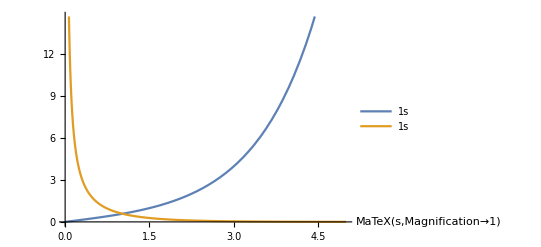

```mathematica
Plot[{BesselI[1,s],BesselK[1,s]},{s,0,5},AxesLabel->(MaTeX[#,Magnification->12/12]&)/@{"s"},PlotLegends->"Expressions",BaseStyle->texStyle]
```

A particular solution can be constructed as  , where the latter expression uses the Lommel function . Note that

```mathematica
Print[ⅈ  ResourceFunction["LommelS"][0,1,ⅈ s]]
```

1/s

The solution to the modified Lommel equation may then be expressed as

See C. H. Ziener & H. P. Schlemmer (2013) The inverse Laplace transform of the modified Lommel functions, Integral Transforms and Special Functions, 24:2, 141-155, DOI: 10.1080/10652469.2012.672324 and https://mathworld.wolfram.com/ModifiedBesselDifferentialEquation.html

#### Apply radial boundary conditions to solve for coefficients and obtain full solution

Now apply the radial boundary conditions: . This yields the system of equations  and . Solve this for  and .

```mathematica
coeffsols = Solve[
Ann*BesselI[1,kn/γ]+Bnn*BesselK[1,kn/γ] -ⅈ  ResourceFunction["LommelS"][0,1,ⅈ kn/γ]==0&& Ann*BesselI[1,χ kn/γ]+Bnn*BesselK[1,χ kn/γ] -ⅈ  ResourceFunction["LommelS"][0,1,ⅈ χ kn/γ]==0,
{Ann,Bnn},
Assumptions->{χ>0,kn>0,γ>0}
];
An = Ann/.coeffsols[[1]];
Bn =Bnn/.coeffsols[[1]];
```

Construct the solution  and check that it satisfies the modified Lommel equation

```mathematica
Unfunc[s_,n_] = -(An*BesselI[1,s] +Bn*BesselK[1,s]) +ⅈ  ResourceFunction["LommelS"][0,1,ⅈ s];
0==FullSimplify[ModLommelEq[Unfunc]]
```

True

Rescale  to construct radial eigenfunctions

```mathematica
inversescaling = {s->ρ kn/γ ,
		kn->π(n-1/2),
		μ->(2 (1+χ))/(kn^2 γ)};
```

```mathematica
anfunc[n_,γ_,χ_] = μ An//.inversescaling//Simplify;
anfunc[n_,γ_,χ_] = μ Bn//.inversescaling//Simplify;
mufunc[n_,γ_,χ_] = μ//.inversescaling//Simplify;
anI1[ρ_,n_,γ_,χ_] = μ An*BesselI[1,s]//.inversescaling//Simplify;
bnK1[ρ_,n_,γ_,χ_] = μ Bn*BesselK[1,s]//.inversescaling//Simplify;
muT01[ρ_,n_,γ_,χ_]=ⅈ μ ResourceFunction["LommelS"][0,1,ⅈ s]//.inversescaling//Simplify;
unfunc[ρ_,n_,γ_,χ_] = μ Unfunc[s,n]//.inversescaling//Simplify;
```

To clean things up, define  and define constants for the the modified Bessel functions of constant argument

```mathematica
OmegaCleanup = Solve[kn==(n-1/2) π,n][[1]];
ConstantBesselCleanup={BesselK[1,kn/γ]->C1,BesselK[1,(χ kn)/γ]->C2,BesselI[1,kn/γ]->C3,BesselI[1,(χ kn)/γ]->C4};
```

```mathematica
Print[(An/(γ/(kn χ))//Apart//Simplify)*γ/(kn χ)]
Print[(Bn/(γ/(kn χ))//Apart//Simplify)*γ/(kn χ)]
Print[Bn/An//Simplify]
```

(γ (BesselK[1,kn/γ]-χ BesselK[1,(kn χ)/γ]))/(kn χ (BesselI[1,(kn χ)/γ] BesselK[1,kn/γ]-BesselI[1,kn/γ] BesselK[1,(kn χ)/γ]))

(γ (BesselI[1,kn/γ]-χ BesselI[1,(kn χ)/γ]))/(kn χ (-BesselI[1,(kn χ)/γ] BesselK[1,kn/γ]+BesselI[1,kn/γ] BesselK[1,(kn χ)/γ]))

(BesselI[1,kn/γ]-χ BesselI[1,(kn χ)/γ])/(-BesselK[1,kn/γ]+χ BesselK[1,(kn χ)/γ])

The radial solution may then be expressed as

where

,

    and

Note that the nth particular solution  is simply the nth coefficient of the generalized Fourier expansion of the 1D Low-Re Shallow solution! i.e.

Check the above statement:

```mathematica
muT01[ρ,n,γ,χ]==2 ∫_0^1 ((1+χ)(2 ζ-ζ^2))/(2ρ)*Sin[(-1/2+n) π ζ]ⅆζ//Simplify[#,Element[n,Integers]]&
```

True

Observe how (the normalized average in  of) the radial eigenfunctions  decay with

```mathematica
unmaxnorm[n_,γ_,χ_] =MaxValue[{unfunc[r,n,γ,χ],χ≤r≤1},r]/MaxValue[{unfunc[r,1,γ,χ],χ≤r≤1},r];
Logunmaxnorm[n_,γ_,χ_]= Log[unmaxnorm[n,γ,χ]];
```

```mathematica
Manipulate[plt=Show[ListLogLogPlot[Table[unmaxnorm[n,γ,χ],{n,1,7}]],LogLogPlot[Evaluate[Exp[logα] n^β/.FindFit[Thread[{Table[Log[n],{n,1,10}],Table[Logunmaxnorm[n,γ,χ],{n,1,10}]}],β logn+logα,{logα,β},logn]],{n,1,7},PlotLegends->(MaTeX[#,Magnification->12/12]&)/@{DecimalForm[Evaluate[Exp[logα] n^β/.FindFit[Thread[{Table[Log[n],{n,1,10}],Table[Logunmaxnorm[n,γ,χ],{n,1,10}]}],β logn+logα,{logα,β},logn]],DefaultPrintPrecision->3]},PlotStyle->{Dashed,Automatic}],Frame->True,FrameLabel->(MaTeX[#,Magnification->12/12]&)/@{"n","\\frac{\\max  \\left| \hat{u}_n \\tilde{r}\\right| }{\\max  \\left| \hat{u}_1 \\tilde{r}\\right| }"},PlotLabel->Row[{"Uniform convergence of u_n(r̃)",", γ=",γ,", χ=",χ}],BaseStyle->texStyle],Button["Export",Export["/Users/cydavid/Documents/UCLA/SPINLab/Magneto-Couette/figures/Theory/2D-radial-modes-normed.pdf",plt]],{plt,ControlType->None},{{χ,0.4},0.1,0.9},{{γ,0.03},0.025,0.2}]
```

Construct the full solution as

```mathematica
uBeigensoln[ρ_,ζ_,n_,γ_,χ_] = Sin[π(n-1/2)ζ]*unfunc[ρ,n,γ,χ];
uBSoln[ρ_,ζ_,l_,γ_,χ_] = Sum[uBeigensoln[ρ,ζ,n,γ,χ],{n,1,l}];
```

or

where

,

    and

### Time-varying solution

#### IVP

```mathematica
Print["Time-varying:       ",(0==magStkUnsteady)//.splitcleanup]
Print["Initial condition:  ",((IC//.split//.splitcleanup)[[1]][[2]]==ICUnsteadyExpr)//.splitcleanup]
```

Time-varying:       0==γ^2 (u'/(r̃)^2-(d_(r̃)[u'])/(r̃)-d_(r̃)^2[u'])+Re_C d_(t̃)[u']-d_(z̃)^2[u']

Initial condition:  u'[0,r̃,θ,z̃]==-ū

#### Separation of variables:

```mathematica
SepExpr =(magStkUnsteady//.{uP->(T[#1]*R[#2]*Z[#4]&)})/(R[ρ] T[τ] Z[ζ])//Apart//Collect[#,T[τ]]&;
SepEqn=AddSides[SepExpr==0,-(γ^2/ρ^2-(γ^2 R'[ρ])/(ρ R[ρ])-(γ^2 R''[ρ])/R[ρ]-Z''[ζ]/Z[ζ])]
```

(ReC T'[τ])/T[τ]==-γ^2/ρ^2+(γ^2 R'[ρ])/(ρ R[ρ])+(γ^2 R''[ρ])/R[ρ]+Z''[ζ]/Z[ζ]

#### Time ODE

```mathematica
TODE = SepEqn[[1]]==-λ^2
RZPDE = AddSides[SepEqn[[2]]==-λ^2,λ^2-(-γ^2/ρ^2+(γ^2 R'[ρ])/(ρ R[ρ])+(γ^2 R''[ρ])/R[ρ])]

Tfunc[τ_,λ_]=DSolveValue[TODE,T[τ],τ][[1]]
```

(ReC T'[τ])/T[τ]==-λ^2

λ^2+Z''[ζ]/Z[ζ]==γ^2/ρ^2-(γ^2 R'[ρ])/(ρ R[ρ])-(γ^2 R''[ρ])/R[ρ]

ⅇ^(-(λ^2 τ)/ReC)

#### Vertical ODE

```mathematica
ZODE=RZPDE[[1]]==μ^2 γ^2
RODE=((RZPDE[[2]]/γ^2)//Simplify)==μ^2
```

λ^2+Z''[ζ]/Z[ζ]==γ^2 μ^2

(R[ρ]-ρ (R'[ρ]+ρ R''[ρ]))/(ρ^2 R[ρ])==μ^2

Check that vertical BCs are satisfied

```mathematica
Zfunc[ζ_,λ_,μ_]=Sin[√(λ^2-μ^2 γ^2) ζ]
ZODE//.{Z->(Zfunc[#1,λ,μ]&)}
lambdaRel[n_,μ_]=√(π^2(-1/2+n)^2 +γ^2 μ^2);
Zfuncn[ζ_,n_]=Assuming[n>1/2,Simplify[Zfunc[ζ,lambdaRel[n,μ],μ]]]
0==Zfuncn[0,n]
0==Assuming[n∈Integers,Simplify[D[Zfuncn[ζ,n],ζ]//.{ζ->1}]]
```

Sin[ζ √(λ^2-γ^2 μ^2)]

True

Sin[1/2 (-1+2 n) π ζ]

True

True

#### Radial ODE

```mathematica
Rfunc[ρ_,μ_]=DSolveValue[{RODE},R[ρ],ρ]
```

BesselJ[1,μ ρ] C[1]+BesselY[1,μ ρ] C[2]

Apply radial BCs and use solvability condition to determine μ

```mathematica
coeffsystem = {Rfunc[χ,μ]==0,Rfunc[1,μ]==0};
muMatrix = (CoefficientArrays[coeffsystem,{C[1],C[2]}]//Normal)[[2]];
detMatrix[χ_] = Det[muMatrix];
solvCond[χ_] = detMatrix[χ] ==0
```

BesselJ[1,μ χ] BesselY[1,μ]-BesselJ[1,μ] BesselY[1,μ χ]==0

μ_m is found as the m-th root of

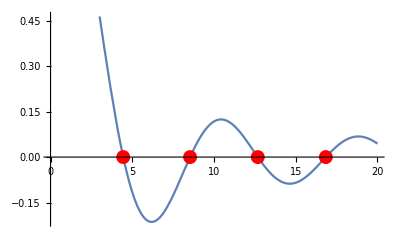

```mathematica
Off[Reduce::ratnz]
Off[Reduce::nint]
Off[General::stop]

muValues[χ_,low_,upp_]:= Flatten[Values[{ToRules[Reduce[solvCond[χ]&&low<μ<upp,μ]]}]];

χ1=0.25;
lowlim = 1;
upplim=20;
Plot[detMatrix[χ1] ,{μ,0,upplim},Epilog->{Red,PointSize[0.025],Point[{μ,detMatrix[χ1] }]/.{ToRules[Reduce[solvCond[0.25]&&lowlim<μ<upplim,μ]]}}]
```

Reduce the solvability condition:

```mathematica
Reduce[solvCond[χ]]
```

(BesselY[1,μ χ]==0&&BesselY[1,μ]==0)||(BesselY[1,μ χ]≠0&&BesselJ[1,μ]==(BesselJ[1,μ χ] BesselY[1,μ])/BesselY[1,μ χ])||(BesselY[1,μ χ]==0&&BesselY[1,μ]≠0&&BesselJ[1,μ χ]==0)

Note that BesselY[1,μ χ]≠0 for nontrivial C[1] and C[2]. Using this fact, we may solve for the ratio of coefficients:

```mathematica
coeffSoln2 = Solve[coeffsystem [[2]],C[2]][[1]];
coeffRatio = (C[2]/C[1])//.coeffSoln2 
detMatrix[χ]==AddSides[Assuming[BesselY[1,μ]/ C[1]≠0,Simplify[MultiplySides[coeffsystem [[1]]//.coeffSoln2 ,BesselY[1,μ]/ C[1]]]],-BesselJ[1,μ] BesselY[1,μ χ]][[1]]
```

-BesselJ[1,μ]/BesselY[1,μ]

True

```mathematica
C1 = 1/BesselJ[1,μ];
C2 = -1/BesselY[1,μ];
C2/C1 == coeffRatio
```

True

```mathematica
RfuncEig[ρ_,μ_]=Rfunc[ρ,μ]//.{ C[1]->C1, C[2]->C2}
```

BesselJ[1,μ ρ]/BesselJ[1,μ]-BesselY[1,μ ρ]/BesselY[1,μ]

```mathematica
uPEigenFunc[τ_,ρ_,ζ_,γ_,χ_,ReC_,μ_,n_]=RfuncEig[ρ,μ]Zfuncn[ζ,n]Tfunc[τ,lambdaRel[n,μ]]
```

ⅇ^(-(((-1/2+n)^2 π^2+γ^2 μ^2) τ)/ReC) (BesselJ[1,μ ρ]/BesselJ[1,μ]-BesselY[1,μ ρ]/BesselY[1,μ]) Sin[1/2 (-1+2 n) π ζ]

The solution may be expressed as

Now enforce the initial condition

Using the orthogonality of vertical eigenfunctions  leaves a general Bessel series of first order on the left side:

or, more succinctly

Then, we find the coefficients as

where

First, compute . See DLMF https://dlmf.nist.gov/10.22 Eq. 10.22.5

```mathematica
RNormIntegrand = ρ(RfuncEig[ρ,μ])^2//Apart
```

(ρ BesselJ[1,μ ρ]^2)/BesselJ[1,μ]^2-(2 ρ BesselJ[1,μ ρ] BesselY[1,μ ρ])/(BesselJ[1,μ] BesselY[1,μ])+(ρ BesselY[1,μ ρ]^2)/BesselY[1,μ]^2

```mathematica
FirstTermDefInt=Integrate[RNormIntegrand [[1]],{ρ,χ,1}];
LastTermDefInt=Integrate[RNormIntegrand [[3]],{ρ,χ,1}];
CrossTermIndefInt=-1/(2BesselJ[1,μ] BesselY[1,μ])ρ^2(2BesselJ[1,μ ρ]BesselY[1,μ ρ]-BesselJ[0,μ ρ]BesselY[2,μ ρ]-BesselJ[2,μ ρ]BesselY[0,μ ρ]);

RNormIntegrand [[2]]==D[CrossTermIndefInt,ρ]//FullSimplify
CrossTermDefInt=(CrossTermIndefInt//.{ρ->1}) - (CrossTermIndefInt//.{ρ->χ} );

RNorm =(FirstTermDefInt+CrossTermDefInt+LastTermDefInt)//Apart//FullSimplify;
```

True

```mathematica
TeXForm[(Integrate[RNormIntegrand [[1]],ρ]+CrossTermIndefInt+Integrate[RNormIntegrand [[1]],ρ])//.splitcleanup];
```

Now, compute . See DLMF https://dlmf.nist.gov/10.22 Eq. 10.22.5

```mathematica
uhatn[ρ_]=(2 (1+χ))/(kn^2 γ)(-(an*BesselI[1,s] +bn*BesselK[1,s]) +ⅈ  ResourceFunction["LommelS"][0,1,ⅈ s])//.{s->ρ kn/γ};
uhatRinner = Assuming[{χ∈Reals,0<χ<1},FullSimplify[Integrate[ρ RfuncEig[ρ,μ]uhatn[ρ],{ρ,χ,1}]]]//Collect[#,{an,bn}]&;
```

```mathematica
Iexpr = Integrate[ρ RfuncEig[ρ,μ]BesselI[1,ρ kn/γ],ρ];
"\langle I_1(k_n \\tilde{r}/\gamma),R_m(\\tilde{r})\\rangle = "<>StringReplace[ToString[TeXForm[Iexpr]],{"\\text{kn}"->"k_n","\\rho"->"\\tilde{r}"}]<>"\\lvert_{\\rho=\\chi}^{\\rho=1}";
```

```mathematica
Kexpr = (γ ρ (γ μ BesselK[1,(kn ρ)/γ] (BesselJ[2,μ ρ]  BesselY[1,μ]-BesselJ[1,μ]  BesselY[2,μ ρ])+kn BesselK[2,(kn ρ)/γ] (-BesselJ[1,μ ρ] BesselY[1,μ]+BesselJ[1,μ] BesselY[1,μ ρ])))/((kn^2+γ^2 μ^2) BesselJ[1,μ] BesselY[1,μ]);
(Kexpr ==Integrate[ρ RfuncEig[ρ,μ]BesselK[1,ρ kn/γ],ρ])//FullSimplify
"\langle K_1(k_n \\tilde{r}/\gamma),R_m(\\tilde{r})\\rangle = "<>StringReplace[ToString[TeXForm[Kexpr]],{"\\text{kn}"->"k_n","\\rho"->"\\tilde{r}"}]<>"\\lvert_{\\rho=\\chi}^{\\rho=1}";
```

True

```mathematica
TeXForm[Integrate[ρ RfuncEig[ρ,Subscript[μ, m]]1/(ρ),ρ]//FullSimplify]//.splitcleanup;
```

```mathematica
Cnm[μ_,n_,γ_,χ_] = (-uhatRinner/RNorm)//.{kn->(n-1/2) π,an->An,bn->Bn};
```

```mathematica
uPEigenSoln[τ_,ρ_,ζ_,γ_,χ_,ReC_,n_,μ_] := Cnm[μ,n,γ,χ]uPEigenFunc[τ,ρ,ζ,γ,χ,ReC,μ,n];
uPSoln[τ_,ρ_,ζ_,γ_,χ_,ReC_,Nn_,Nm_,muList_] := Sum[Sum[uPEigenSoln[τ,ρ,ζ,γ,χ,ReC,n,muList[[m]]],{m,1,Nm}],{n,1,Nn}];
```

Check that solution satisfies the PDE

```mathematica
0==(magStkUnsteady//.{uP->(uPEigenSoln[#1,#2,#4,γ,χ,ReC,n,μ]&)})//FullSimplify
```

True

Visually check that solution satisfies initial condition

```mathematica
χplot=0.25;
muL = muValues[χplot,1,20]
```

{4.44751,8.53692,12.679,16.8416}

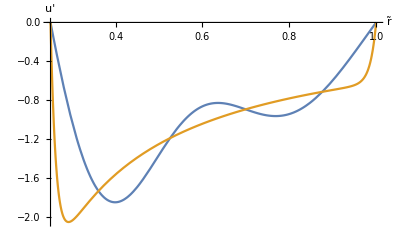

```mathematica
ReCplot = 1;
τplot = 0*(4 ReCplot)/π^2;
Nnplot =4;
Nmplot=4;
rprof = Plot[{uPSoln[τplot,ρ,1,0.02,χplot,ReCplot,Nnplot,Nmplot,muL],-uBSoln[ρ,1,4,0.02,χplot]},{ρ,χplot,1},PlotStyle->{ColorData[97][1],ColorData[97][2]},AxesLabel->{"r̃","u'"}];
zprof = Plot[{uPSoln[τplot,(1+χplot)/2,ζ,0.02,χplot,ReCplot,Nnplot,Nmplot,muL],-uBSoln[(1+χplot)/2,ζ,4,0.02,χplot]},{ζ,0,1},PlotStyle->{ColorData[97][1],ColorData[97][2]},AxesLabel->{"z̃","u'"},PlotLegends->{"u' at  t=0", "-ū"}];
Show[GraphicsGrid[{{rprof,zprof}}],PlotLabel->Row[{"N_n= ",Nnplot,",    N_m= ",Nmplot}],ImageSize->Large]
```